```mathematica
ZrC phonon DOS analysis (a =4.575Ångstrom) ;
```

```mathematica
System details;
```

```mathematica
ClearAll;
(*SYSTEM_DETAILS,
alatt=4.575Ang ZrC harmonic phonon DOS, 
alatt corresponds to a slightly smaller than equilibrium volume at any temperature,
i.e. slightly smaller than the Volume at T=0K,  a compressive strain of the order couple percent at zero temperature *)
```

```mathematica
Units/definitions;
```

```mathematica
(*UNITS,
phonon Data read in in THz,
Converted to meV by 1THz=4.14meV,
Convert temperature from Kelvin to meV via 1K=8.6173324*10^-5eV,
2by2by2 supercell 64 atoms
*)
THz2meV = 4.14;
K2meV=0.086173324;
Natoms=64;
```

```mathematica
Import data - normal total phonon DOS;
```

Phonon DOS in discrete data in THz units:

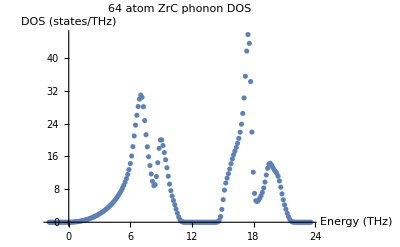

Number of data points in phonon DOS data:

201

```mathematica
(*Import the harmonic phonon DOS*)

SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZPE"];
phononDOSdata=ReadList["energy_dos.dat",{Number, Number}];
"Phonon DOS in discrete data in THz units:"
ListPlot[phononDOSdata,AxesLabel->{"Energy\n (THz)","DOS (states/THz)"},PlotLabel->"64 atom ZrC phonon DOS"]
"Number of data points in phonon DOS data:"
length=Length[phononDOSdata]
phononDOSdata;
```

Phonon DOS in discrete data in THz units:

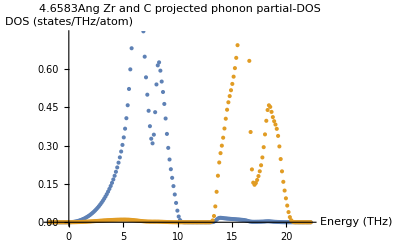

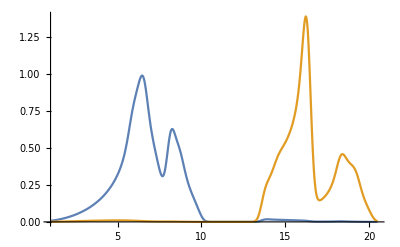

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
phononZrPDOSdata=ReadList["Zr_atom1_4.65837.pdos",{Number, Number}];
phononCPDOSdata=ReadList["C_atom1_4.65837.pdos",{Number, Number}];
"Phonon DOS in discrete data in THz units:"
ListPlot[{phononZrPDOSdata,phononCPDOSdata},AxesLabel->{"Energy\n (THz)","DOS (states/THz/atom)"},PlotLabel->"4.6583Ang Zr and C projected phonon partial-DOS"]
Plot[{Interpolation[phononZrPDOSdata][x],Interpolation[phononCPDOSdata][x]},{x,1,20.5},PlotRange->All]
```

```mathematica
Partial DOS comparison - projections of phonon DOS against one Zr and against one C atom;
```

Phonon DOS in discrete data in THz units:

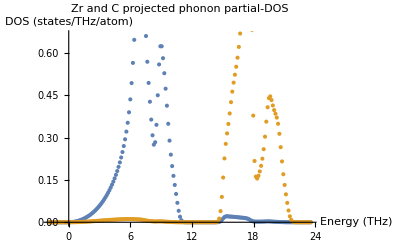

Conclusion: 
1)comparing the PDOS with total DOS above, it is clear that in the lower band in the total DOS is basically pure Zr, and the upper band pure C. Zr_mass = 3.33*C_mass, so I suppose that makes sense
2)If the phonon DOS for Zr and C have distinct DOS separated by an energy gap, are they basically uncoupled, in which case an Einstein oscillator is a good description?

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
phononZrPDOSdata=ReadList["Zr_atom1_4.575.pdos",{Number, Number}];
phononCPDOSdata=ReadList["C_atom1_4.575.pdos",{Number, Number}];
"Phonon DOS in discrete data in THz units:"
ListPlot[{phononZrPDOSdata,phononCPDOSdata},AxesLabel->{"Energy\n (THz)","DOS (states/THz/atom)"},PlotLabel->"Zr and C projected phonon partial-DOS"]
"Conclusion: 
1)comparing the PDOS with total DOS above, it is clear that in the lower band in the total DOS is basically pure Zr, and the upper band pure C. Zr_mass = 3.33*C_mass, so I suppose that makes sense
2)If the phonon DOS for Zr and C have distinct DOS separated by an energy gap, are they basically uncoupled, in which case an Einstein oscillator is a good description?"
```

```mathematica
Interpolate data;
```

```mathematica
(*Definie minimum and maximum phonon energies, in THz and meV, and Interpolate the discete phonon data to make function for later analysis*)
"Minimum phonon energy in THz (nb, DOS below zero is practically negligible:"
EminTHz=phononDOSdata[[1,1]]
"Minimum phonon energy in meV (nb, DOS below zero is practically negligible:"
Emin=EminTHz*THz2meV
"Maximum phonon enegry in THz:"
EmaxTHz=phononDOSdata[[length,1]]
"Maximum phonon enegry in meV:"
Emax=EmaxTHz*THz2meV
interpolDOS=Interpolation[phononDOSdata];
```

Minimum phonon energy in THz (nb, DOS below zero is practically negligible:

-1.89959

Minimum phonon energy in meV (nb, DOS below zero is practically negligible:

-7.86428

Maximum phonon enegry in THz:

23.5739

Maximum phonon enegry in meV:

97.5961

```mathematica
Plot phonon DOS;
```

Phonon DOS ZrC 202020kp 64 atom 222supercell:

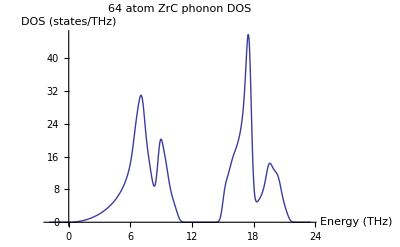

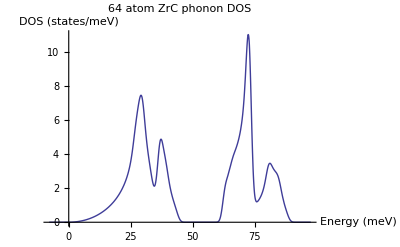

```mathematica
(*Plot interpolated phonon DOS*)
DOSTHz[energy_]:=If[EminTHz<energy<EmaxTHz,interpolDOS[energy],0.0];
DOS[energy_]:=If[Emin<energy<Emax,(1/THz2meV)*interpolDOS[energy/THz2meV],0.0];
"Phonon DOS ZrC 202020kp 64 atom 222supercell:"
Plot[DOSTHz[energy],{energy,EmaxTHz,EminTHz},AxesLabel->{"Energy\n (THz)","DOS (states/THz)"},PlotLabel->"64 atom ZrC phonon DOS"]
Plot[DOS[energy],{energy,Emax,Emin},AxesLabel->{"Energy\n (meV)","DOS (states/meV)"},PlotLabel->"64 atom ZrC phonon DOS"]
```

```mathematica
Number of harmonic states;
```

```mathematica
(*Integrate DOS(energy) function, and check not mad - should be 3n harmnic modes with n=64 atom cell...*)
sumAllModes=NIntegrate[DOS[energy],{energy,Emin,Emax}];
"N_atoms=N_modes=64*3:"
NIntegrate[DOS[energy],{energy,Emin,Emax}]
```

N_atoms=N_modes=64*3:

192.

```mathematica
Zero point energy;
```

```mathematica
(*Find the zero point energy ZPE - come back to units*)
"The vibrational zero point energy per atom in meV:"
perAtomZPE=NIntegrate[DOS[energy]*energy*0.5/Natoms,{energy,Emin,Emax}]
```

The vibrational zero point energy per atom in meV:

77.2712

```mathematica
Split the DOS into two parts for later Einstein oscillator frequencies;
```

```mathematica
(*Define point about which to split the DOS, into 2 parts in this case*)
energyCentrePoint=0.5*(Emax-Emin);
dataCentrePoint=Round[length*energyCentrePoint/Emax];
(*Check phonon DOS is zero at the a 'centre point' for band1/band2 integration limits - Yes*)
phononDOSdata[[dataCentrePoint,2]];
band1DOS[energy_]:=If[Emin<energy<energyCentrePoint,DOS[energy],0.0];
band2DOS[energy_]:=If[energyCentrePoint<energy<Emax,DOS[energy],0.0];
```

```mathematica
Lower energy band average energy;
```

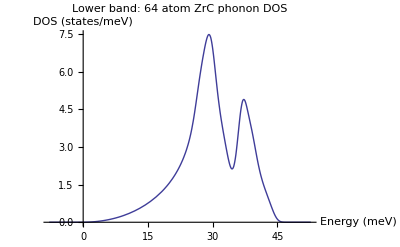

Number of modes in the lower band:

96.

Simple Mean band energy:

26.3651

Mode-type average energy (the tallest peak of this lower band):

29.135

Median energy of lower band, i.e. the energy integrated limit that gives half of the total number of band modes:

29.5684

```mathematica
(*Integrate DOS of band 1 and find energy 'centre of mass'*)
Plot[band1DOS[energy],{energy,Emin,energyCentrePoint},AxesLabel->{"Energy\n (meV)","DOS (states/meV)"},PlotLabel->"Lower band:\n 64 atom ZrC phonon DOS"]
"Number of modes in the lower band:"
sumBand1Modes=NIntegrate[band1DOS[energy],{energy,Emin, energyCentrePoint}]
(*
3ways to find the centre of this section of DOS we are analysing:,
1- Find the 'mean' energy, i.e. one quarter of the way up the phonon DOS energy scale,
2- Find the 'mode' energy, phonon energy value for the peak maximum,
3- Find 'median' energy, ie the energy point where the intergated DOS value is equal to half the modes in the band, namely 48 - probably the best way
*)
"Simple Mean band energy:"
band1Middle=energyCentrePoint/2
(*Band centre defined as mean*)
"Mode-type average energy (the tallest peak of this lower band):"
band1ModeEnergy=InverseFunction[band1DOS][MaxValue[band1DOS[energy],{energy}]]
Off[NIntegrate::nlim];
integrateMedian[lowerLimit_,band1median_]:=NIntegrate[DOS[energy],{energy,lowerLimit,band1median}];
"Median energy of lower band, i.e. the energy integrated limit that gives half of the total number of band modes:"
band1median=band1median/.FindRoot[integrateMedian[Emin,band1median]-48==0,{band1median,1}]
```

```mathematica
High energy band average energy;
```

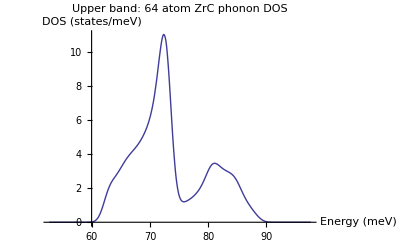

Number of modes in the lower band:

96.

Simple Mean band energy for lower band

79.0953

Mode-type average energy (ie tallest peak) of the lower band:

72.3788

Median energy of lower band, i.e. the energy integrated limit that gives half of the total number of band modes:

72.1665

```mathematica
(*Integrate DOS of band 1 and find energy 'centre of mass'*)
Plot[band2DOS[energy],{energy,energyCentrePoint,Emax},AxesLabel->{"Energy\n (meV)","DOS (states/meV)"},PlotLabel->"Upper band:\n 64 atom ZrC phonon DOS"]
"Number of modes in the lower band:"
sumBand1Modes=NIntegrate[band2DOS[energy],{energy,energyCentrePoint,Emax}]
(*
3ways to find the centre of a band,
1- Find the 'mean' energy, i.e. one quarter of the way up the phonon DOS energy scale,
2- Find the 'mode' energy, phonon energy value for the peak maximum,
3- Find 'median' energy, ie the energy point where the intergated DOS value is equal to half the modes in the band (48). As an initial guess in the rootFinder algorithm, use the Mode band energy calculated prior
*)
"Simple Mean band energy for lower band"
band2Middle=1.5*energyCentrePoint
(*Band centre defined as mean*)
"Mode-type average energy (ie tallest peak) of the lower band:"
band2ModeEnergy=InverseFunction[DOS][MaxValue[DOS[energy],{energy}]]
Off[FindRoot::lstol];
"Median energy of lower band, i.e. the energy integrated limit that gives half of the total number of band modes:"
integrateMedian2[band2median_]:=NIntegrate[band2DOS[energy],{energy,energyCentrePoint,band2median}];
findRoot[initialGuess_]:=FindRoot[integrateMedian2[band2median]-48==0,{band2median,initialGuess}]
band2median=band2median/.findRoot[band2ModeEnergy]
```

```mathematica
"Simple Einstein oscillator:"
eisteinOscillatorsSimple={band1Middle,band2Middle}
"Mode-type Einstein oscillator:"
eisteinOscillatorsMode={band1ModeEnergy,band2ModeEnergy}
"Median-type Einstein oscillator:"
eisteinOscillatorsMedian={band1median,band2median}
```

Simple Einstein oscillator:

{26.3651,79.0953}

Mode-type Einstein oscillator:

{29.135,72.3788}

Median-type Einstein oscillator:

{29.5684,72.1665}

```mathematica
DOS temperature dependence;
```

```mathematica
(*Plot Bose-Einstein, DOS and DOS*Bose-Einstein together to try to aid intuition*)
(*Define functions*)
boseEinstein[energymeV_,tempmeV_]:=1/(Exp[energymeV/tempmeV]-1)
dosBoseEinstein[energymeV_,tempmeV_]:=DOS[energymeV]*boseEinstein[energymeV,tempmeV]

Manipulate[Show[
Plot[{boseEinstein[energymeV,tempmeV],DOS[energymeV],dosBoseEinstein[energymeV,tempmeV]},{energymeV,0,94},PlotRange-> {{0,94},{0,9+tempmeV/4}},PlotStyle->{{Hue[0.6],Thick},{Hue[1.0],Thick},{Hue[0.3],Thick}},AxesLabel->{"Energy (meV)","Density or Particle number"},ImageSize -> 450 ,PlotLegends->SwatchLegend[{"<n(T)>","DOS","DOS*<n(T)>"}],PlotLabel -> Row[{ Style["ZrC Phonon DOS in Temperature", Large]}]
]],{{tempmeV,25.85,"Temperature (meV)\n\n Reference points:\n Room Temperature ~ 300K = 25.85meV\n ZrC Melting Point ~ 3805K = 327.9meV"},5,328,Appearance->"Labeled"},  ControllerLinking -> True,Initialization :> { Attributes[PlotRange] = {ReadProtected}}]
```

```mathematica
Energy of phonon DOS;
```

```mathematica
(*Plot the harmonic phonon energy pre-integration, i.e. integrand, to gain some intuition*)
energyIntegrand[energymeV_,tempmeV_]:=DOS[energymeV]*energymeV*(boseEinstein[energymeV,tempmeV]+0.5)
entropyIntegrand[energymeV_,tempmeV_]:=-DOS[energymeV]*(Log[1-Exp[-energymeV/tempmeV]]-(energymeV/tempmeV)*((Exp[-energymeV/tempmeV])/(1-Exp[-energymeV/tempmeV])))
Manipulate[Show[
Plot[{DOS[energymeV],energyIntegrand[energymeV,tempmeV]},{energymeV,0,94},PlotRange-> {{0,94},{0,50+120*(boseEinstein[10,tempmeV]+0.5)}},PlotStyle->{{Hue[0.6],Thick},{Hue[1.0],Thick}},ImageSize -> 450 ,PlotLegends->SwatchLegend[{"DOS","Energy integrand"}],AxesLabel->{"Energy (meV)","DOS or Energy*DOS"},PlotLabel -> Row[{ Style["ZrC phonons in temperature", Large]}]
]],{{tempmeV,25.85,"Temperature (meV)\n\n Reference points:\n Room Temperature ~ 300K = 25.85meV\n ZrC Melting Point ~ 3805K = 327.9meV"},5,328,Appearance->"Labeled"},  ControllerLinking -> True,Initialization :> { Attributes[PlotRange] = {ReadProtected}}]
```

Plot::prng: Value of option PlotRange -> {{0, 94}, {0, 50 + 120\ (0.5  + boseEinstein[10, 5.])}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
Entropy of phonon DOS;
```

```mathematica
(*Plot entropy before it is integrated over energy*)
Manipulate[Show[
Plot[{DOS[energymeV],entropyIntegrand[energymeV,tempmeV]},{energymeV,0,94},PlotRange-> {{0,94},{0,30}},PlotStyle->{{Hue[0.6],Thick},{Hue[1.0],Thick}},ImageSize -> 450 ,PlotLegends->SwatchLegend[{"DOS","Entropy integrand"}],AxesLabel->{"Energy (meV)","DOS or Entropy*DOS"},PlotLabel -> Row[{ Style["ZrC phonons in temperature", Large]}]
]],{{tempmeV,25.85,"Temperature (meV)\n\n Reference points:\n Room Temperature ~ 300K = 25.85meV\n ZrC Melting Point ~ 3805K = 327.9meV"},5,328,Appearance->"Labeled"},  ControllerLinking -> True,Initialization :> { Attributes[PlotRange] = {ReadProtected}}]
```

```mathematica
Entropy vs temperature;
```

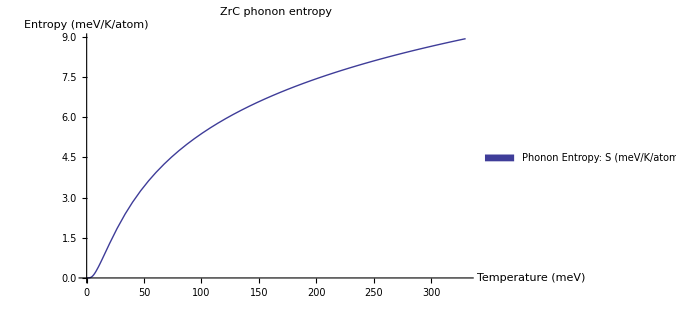

```mathematica
(*Integrate over the whole DOS spectrum *)
phononEntropy[tempmeV_]:=NIntegrate[entropyIntegrand[energymeV,tempmeV]/Natoms,{energymeV,0,Emax},Method->{Automatic,"SymbolicProcessing"->0}]
Plot[phononEntropy[tempmeV],{tempmeV,0,330},ImageSize -> 500 ,PlotStyle->Thick,PlotLegends->SwatchLegend[{"Phonon Entropy: S (meV/K/atom)"}],AxesLabel->{"Temperature (meV)","Entropy (meV/K/atom)"},PlotLabel -> Row[{ Style["ZrC phonon entropy", Large]}]]
```

```mathematica
Free energy vs temperature;
```

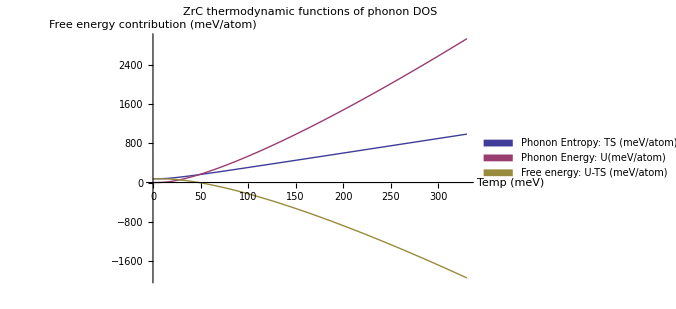

```mathematica
phononEnergy[tempmeV_]:=NIntegrate[energyIntegrand[energymeV,tempmeV]/Natoms,{energymeV,0,Emax},Method->{Automatic,"SymbolicProcessing"->0}]
phononFree[tempmeV_]:=phononEnergy[tempmeV]-phononEntropy[tempmeV]*tempmeV;
Off[NIntegrate::ncvb]
Plot[{phononEnergy[tempmeV],phononEntropy[tempmeV]*tempmeV,phononEnergy[tempmeV]-phononEntropy[tempmeV]*tempmeV},{tempmeV,0,330},ImageSize -> 500 ,PlotStyle->Thick,PlotLegends->SwatchLegend[{"Phonon Entropy:\n TS (meV/atom)","Phonon Energy:\n U(meV/atom)","Free energy:\n U-TS (meV/atom)"}],AxesLabel->{"Temp\n (meV)","Free energy contribution\n (meV/atom)"},PlotLabel -> Row[{ Style["ZrC thermodynamic functions of phonon DOS", Medium]}]]
```

```mathematica
Free energy vs temperature;
```

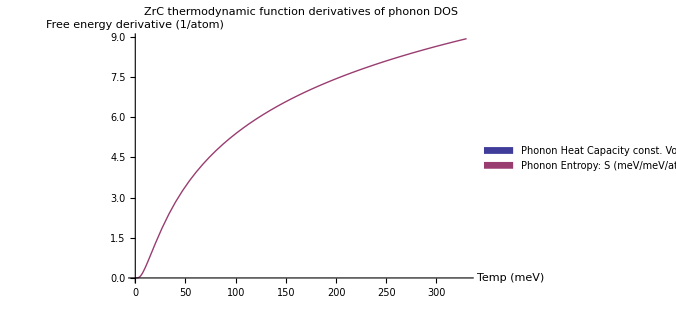

```mathematica
Off[NIntegrate::ncvb]
phononHeatCapacityV[tempmeV_]:=phononFree[tempmeV]';
Plot[{phononHeatCapacityV[tempmeV],phononEntropy[tempmeV]},{tempmeV,0,330},ImageSize -> 500 ,PlotStyle->Thick,PlotLegends->SwatchLegend[{"Phonon Heat Capacity const. Volume:\n Cv (meV/meV/atom (dimensionless))","Phonon Entropy:\n S (meV/meV/atom (dimensionless))"}],AxesLabel->{"Temp\n (meV)","Free energy derivative (1/atom)"},PlotLabel -> Row[{ Style["ZrC thermodynamic function derivatives of phonon DOS", Medium]}]]
```